```mathematica
γ[v_]:=1/(√(1-v^2))
```

Here is the general solution showing the path of a uniformly-accelerated object:

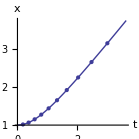

```mathematica
x[τ_]=Cosh[g τ]/g;
t[τ_]=Sinh[g τ]/g;
ParametricPlot[{t[τ],x[τ]}/.g->1, {τ, 0, 2},AxesLabel->{t,x}, Mesh->10]
```

The non-parametric version looks like this:

(√(1+g^2 t^2))/g

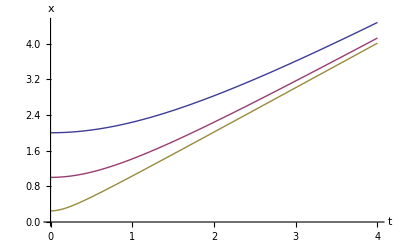

```mathematica
x1[t_]=Cosh[ArcSinh[g t]]/g
Plot[{x1[t]/.g->0.5, x1[t]/.g->1, x1[t]/.g->4},{t, 0, 4},AxesLabel->{t,x}]
```

This has an x-offset and assumes the object is starting with v=0.
We would like an equation that tells us, given an initial location x_0, initial speed v_0, and acceleration g, what is the new position x(t)?

In order to start at v_0, we need to compute an offset value for t.

```mathematica
v[t_]=FullSimplify[D[x1[t], t]]
```

(g t)/(√(1+g^2 t^2))

```mathematica
Solve[v[t]==v0, t]
```

{{t→-v0/(√(g^2-g^2 v0^2))},{t→v0/(√(g^2-g^2 v0^2))}}

So tinit is the time at which we must start computing the hyperbolic curve in order to have a given initial velocity v_0:

```mathematica
tinit[v0_]:=v0/(√(-g^2 (-1+v0^2)))
```

Thus the full equation for position looks like this:

```mathematica
x[t_,x0_,v0_,g_]=FullSimplify[x1[t+t0]-x1[t0]+x0]/.t0->tinit[v0]
```

(-√(1-v0^2/(-1+v0^2))+√(1+g^2 (t+v0/(√(-g^2 (-1+v0^2))))^2)+g x0)/g

(Note that γ appears twice in this equation; do the proper substitution to get a nicer-looking form)

Let’s test it out:

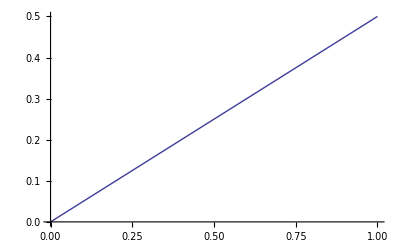

```mathematica
Plot[x[t,0,0.5,0.0001], {t,0,1}]
```

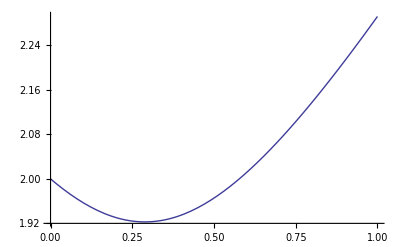

```mathematica
Plot[x[t,2,-0.5,2],{t,0,1}]
```

Looks good. This is good enough for computing the worldline of any object from an inertial reference frame.
However: since the simulation specifies its acceleration program relative to proper time, we want to be able to ask: “if the object accelerates for dτ seconds in its proper time, how long does that take in the inertial reference frame?”

Thus: compute how much proper time τ elapses for reference time t given an acceleration and initial v

```mathematica
τ[t_,v0_]:=ArcSinh[g (t+tinit[v0])]/g-ArcSinh[g tinit[v0]]/g
```

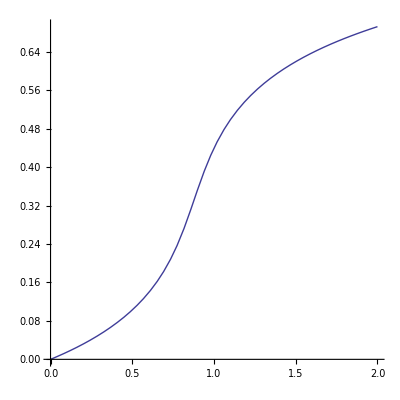

```mathematica
Plot[τ[t,-0.99]/.g->8, {t,0, 2},AspectRatio->1]
```

```mathematica
soln=FullSimplify[Solve[τ[0,v0]+dτ==τ[dt,v0],{dt}]]
```

{{dt→(-(g v0)/(√(-g^2 (-1+v0^2)))+Sinh[dτ g+ArcSinh[(g v0)/(√(-g^2 (-1+v0^2)))]])/g}}

After some simplification, this is the correct equation to use for determining dt given dτ, v_0, and g:

```mathematica
(-v0/(√(1-v0^2))+Sinh[dτ g+ArcSinh[v0/(√(1-v0^2))]])/g/.{dτ->1.0,v0->0.5,g->0.1}
```

1.18552

The trickiest question is: given that we know the worldlines of two accelerated objects (A and B), how do we transform one worldline (A) onto the reference frame of the other (B)? The answer is to use the Lorentz transformation at each point along B’s worldline to select the correct point along A’s worldline.

This is the procedure: for each point on B’s worldline (as seen from intertial frame), draw a line representing everything that B sees at that proper time. Find the hyperbolic segment from A’s worldline that intersects this line, then compute the intersection. Finally, transform the intersected point back into B’s coordinate system using the Lorentz transform.

An identical way of saying this is: for each point on B’s worldline, transform A’s worldline into B’s reference frame using the Lorentz transform for B’s instantaneous velocity. Then, the correct location of A for that proper-time point is where the world line crosses t=0.

This is how we work out the intersection of hyperbola and line.

```mathematica
Clear[Evaluate[Context[]<>"*"]]
```

```mathematica
x[t_,v0_]:=(√(1+(g t+v0 gamma)^2)-gamma)/g
```

```mathematica
soln=Simplify[Solve[x[t-t0, v0]+x0==(t-t0r+vr x0r)/vr, {t}]]
```

{{t→1/(g^2 (-1+vr^2))(-g^2 t0r+g gamma vr+g^2 t0 vr^2-g gamma v0 vr^2-g^2 vr x0+g^2 vr x0r+√(g^2 vr^2 (1+gamma^2 (v0-vr)^2-vr^2+2 g gamma (v0-vr) (-t0+t0r+vr (x0-x0r))+g^2 (t0-t0r+vr (-x0+x0r))^2)))},{t→-1/(g^2 (-1+vr^2))(g^2 t0r-g gamma vr-g^2 t0 vr^2+g gamma v0 vr^2+g^2 vr x0-g^2 vr x0r+√(g^2 vr^2 (1+gamma^2 (v0-vr)^2-vr^2+2 g gamma (v0-vr) (-t0+t0r+vr (x0-x0r))+g^2 (t0-t0r+vr (-x0+x0r))^2)))}}

That’s it. It’s a mess, but it works. There are two solutions; the correct one must be selected based on the sign of g and vr.
(I’m sure this could be simplified. Too lazy.)

```mathematica
params1={gamma->(1-v0^2)^(-1/2)};
params={g->0.00001, vr->-0.1, x0r->5, t0r->15,v0->0.1,x0->0,t0->20};
ind =Mod[ (If[(g/.params)>0,1,0]+If[(vr/.params)<0,1,0]), 2]+1;
t/.soln[[ind]]/.params1/.params
```

15.5445

```mathematica
params={vr->-0.1, x0r->5, t0r->15,v0->-0.1,x0->0,t0->0};
((-vr(x0+v0 t0)+(t0r+x0r vr))/(1+v0))/.params
```

16.1111

```mathematica
soln=Solve[{v0 t+x0-v0 t0==(t-t0r+vr x0r)/vr}, {t}]
```

{{t→(-t0r+t0 v0 vr-vr x0+vr x0r)/(-1+v0 vr)}}

```mathematica
params={vr->0.1, x0r->5, t0r->15,v0->0,x0->5,t0->10};
t/.soln[[1]]/.params
```

15.